# Berechnungen T,C,S

Berechnungen thermodynamischer Größen unter Beinhaltung von Vorfaktoren. Diese Rechnungen wurden das erste mal richtig und größtenteils vollständig in Calc11 gemacht. Wie das Worksheet (hier im Master-Thesis-Ordner), wo die Plots thermodynamischer Größen gemacht wurden (was größtenteils implizite Numerik ist und sehr viel symbolische Graphiksprache von Mathematika, deswegen will ich jenes Worksheet nicht noch weiter verlängern), basiert dieses Worksheet auf Calc11-Worksheets. Konkret gibt es das exzellente Worksheet calc11/critical-radius.nb, von dem einfach große Teile kopiert sind.

```mathematica
h[z_,n_] := 1/(1+(1/z)^(2+n));
Subscript[r, 0]=(1/(1+n))^(1/(2+n));
Subscript[α, 0]=(3+n)/Log[2+n] * Log[(3+n)/2];
Subscript[r, 0,α]=(1/(1+n))^(1/Subscript[α, 0]);
hA[z_,n_] = 1/(1+(1/z)^Subscript[α, 0] / 2)^((3+n)/Subscript[α, 0]);
hα[z_,n_] = 1/(1+(1/z)^α / 2)^((3+n)/α);
```

## Definitionen und erste Rechnungen zu C

```mathematica
M[rH_,H_,n_] := (n+2)/2 MStar^(n+2)Subscript[Ω, n+2] rH^(n+1)/H[rH,n]
```

```mathematica
D[M[rH,H,n],rH]
```

(MStar^(2+n) (1+n) (2+n) rH^n Ω_(2+n))/(2 H[rH,n])-(MStar^(2+n) (2+n) rH^(1+n) Ω_(2+n) H^(1,0)[rH,n])/(2 H[rH,n]^2)

```mathematica
T[rH_,H_,  n_] :=1/(4 Pi rH)(1+n-rH/L(D[H[zz,n],zz]/.{zz-> rH})/H[rH,n])
```

```mathematica
D[T[x,H,n],x]
```

-(1+n-(x H^(1,0)[x,n])/(L H[x,n]))/(4 π x^2)+(-(H^(1,0)[x,n])/(L H[x,n])+(x (H^(1,0)[x,n])^2)/(L H[x,n]^2)-(x H^(2,0)[x,n])/(L H[x,n]))/(4 π x)

```mathematica
CC=D[M[rH,H,n],rH]/D[T[rH,H,n],rH]//FullSimplify
```

-(2 L MStar^(2+n) (2+n) π rH^(2+n) Ω_(2+n) ((1+n) H[rH,n]-rH H^(1,0)[rH,n]))/(L (1+n) H[rH,n]^2-rH^2 (H^(1,0)[rH,n])^2+rH^2 H[rH,n] H^(2,0)[rH,n])

```mathematica
CC/(-4Pi rH^2/(1+n))
```

(L MStar^(2+n) (1+n) (2+n) rH^n Ω_(2+n) ((1+n) H[rH,n]-rH H^(1,0)[rH,n]))/(2 (L (1+n) H[rH,n]^2-rH^2 (H^(1,0)[rH,n])^2+rH^2 H[rH,n] H^(2,0)[rH,n]))

```mathematica
(* Rechunng im Limit *)
CC //. {H[_,_] -> 1, Derivative[_,_][H][__] -> 0}
```

-2 MStar^(2+n) (2+n) π rH^(2+n) Ω_(2+n)

```mathematica
(* Das wird nichts: *)
(* FourierSequenceTransform[-2 MStar^(2+n) (2+n) π rH^(2+n) Subscript[Ω, 2+n],n,ω] *)
```

### Einsetzen von holo in CC (nur der Vollstd. halber)

Ich weiß jetzt nicht mehr genau, wie ich auf die Form von CC in der Thesis selber gekommen bin, daher hier mal... kompakt:

```mathematica
CCThesis=-(4π rH^(n+2))/MStar^(n+2)((n+1)H[rH] - rH H'[rH])/(rH^2 H[rH] H''[rH] -rH^2 H'[rH]^2+(n+1)H[rH]^2)
```

-(4 MStar^(-2-n) π rH^(2+n) ((1+n) H[rH]-rH H'[rH]))/((1+n) H[rH]^2-rH^2 H'[rH]^2+rH^2 H[rH] H''[rH])

```mathematica
CCInsert[h_] :=CCThesis //. {H[x_]-> h[x,n], H'[x_]-> D[h[x,n],x],H''[x_]-> D[h[x,n],{x,2}] }
```

```mathematica
(* Den ganzen Vorfaktorkram rausholen *)
CCInsert[h] /(-(4π rH^(2+n))/MStar^(n+2))// FullSimplify
```

-(((1/rH)^n+rH^2)^2 (-(1/rH)^n+(1+n) rH^2))/((4+n (3+n)) (1/rH)^(-4+n)+(1/rH)^(-2+2 n)-(1+n) rH^6)

```mathematica
CCInsert[hα]  /(-(4π rH^(2+n))/MStar^(n+2))// FullSimplify
```

(2^(-(3+n)/α) (2+(1/rH)^α)^((3+n+α)/α) (-1-n+(1/rH)^α))/(-2 (1+n)+(1/rH)^(2 α)+(1/rH)^α (1+n (-1+α)+3 α))

## Berechnung kritischer Radien (und maximaler Temperaturen)

Die folgenden Rechnungen sind von critical-radius.nb kopiert.

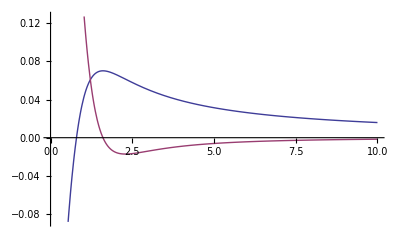

```mathematica
(* Worum geht es? Um das Maxima von T, was die Nullstelle der Ableitung ist. *)
Plot[Evaluate[{T[x,h,n],D[T[x,h,n],x]} /.{L-> 1,n-> 1}],{x,0,10}]
```

### Numerische Bestimmung (für Tabelle in Thesis)

```mathematica
maxH =Table[FindMaximum[T[x,h,n] /. L -> 1,{x,1}],{n,0,7}]
maxT = maxH/.{{yval_,{_-> xval_}}-> yval}
maxhA =Table[FindMaximum[T[x,hA,n]/. L -> 1,{x,1}],{n,0,7}]
extractPos[li_] := NumberForm[#,{3,3}]&/@ (li /. {{_,{_-> xval_}}-> xval})
extractVal[li_] := NumberForm[#,{3,3}]&/@ (li /. {{yval_,{_-> _}}-> yval})
```

{{0.0238958,{x→2.05817}},{0.0701929,{x→1.60329}},{0.124212,{x→1.47529}},{0.182821,{x→1.40858}},{0.244657,{x→1.36369}},{0.308905,{x→1.32986}},{0.375024,{x→1.30288}},{0.442629,{x→1.28062}}}

{0.0238958,0.0701929,0.124212,0.182821,0.244657,0.308905,0.375024,0.442629}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.0243932,{x→1.96928}},{0.0738335,{x→1.46451}},{0.130736,{x→1.34302}},{0.191304,{x→1.29308}},{0.254375,{x→1.26483}},{0.319373,{x→1.24522}},{0.385925,{x→1.2299}},{0.453757,{x→1.21713}}}

```mathematica
Grid[Join[
{{n}~Join~Range[0,7]},
{{"r_C"}~Join~extractPos@maxH},
{{"r_(C, α)"}~Join~extractPos@maxhA},
{{"T_max"}~Join~ extractVal@maxH},
{{"T_(max, α)"}~Join~ extractVal@maxhA}
],Frame-> All]
```

n | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
r_C | 2.060 | 1.600 | 1.480 | 1.410 | 1.360 | 1.330 | 1.300 | 1.280
r_(C, α) | 1.970 | 1.460 | 1.340 | 1.290 | 1.260 | 1.250 | 1.230 | 1.220
T_max | 0.024 | 0.070 | 0.124 | 0.183 | 0.245 | 0.309 | 0.375 | 0.443
T_(max, α) | 0.024 | 0.074 | 0.131 | 0.191 | 0.254 | 0.319 | 0.386 | 0.454

```mathematica
%//TeXForm
```

\begin{array}{ccccccccc}
 n & 0 & 1 & 2 & 3 & 4 & 5 & 6 & 7 \\
 r_C & 2.060 & 1.600 & 1.480 & 1.410 & 1.360 & 1.330 & 1.300 & 1.280 \\
 r_{C,\alpha } & 1.970 & 1.460 & 1.340 & 1.290 & 1.260 & 1.250 & 1.230 & 1.220 \\
 T_{\max } & 0.024 & 0.070 & 0.124 & 0.183 & 0.245 & 0.309 & 0.375 & 0.443 \\
 T_{\max ,\alpha } & 0.024 & 0.074 & 0.131 & 0.191 & 0.254 & 0.319 & 0.386 & 0.454 \\
\end{array}

### Analytische Lösung für Holo

```mathematica
(* Analytisch kann fuer h ein geschlossner Ausdruck gefunden werden: *)
Solve[(D[T[x,h,n],x]/.L-> 1)==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2^(1/(2+n)) (-4-3 n-n^2-(2+n) √(5+2 n+n^2))^(-1/(2+n))},{x→2^(1/(2+n)) (-4-3 n-n^2+(2+n) √(5+2 n+n^2))^(-1/(2+n))}}

Nur die zweite Lösung entspricht reellen Ergebnissen obiger Tabelle (nachgeprüft durch Einsetzen von n), dies ist also das korrekte.

### Analytische Lösung für h_α

```mathematica
(* Analytisch kann fuer Subscript[h, α] mit Subscript[α, 0] kein geschlossener Ausdruck mehr gefunden werden*)
Solve[(D[T[x,hA,n],x]/. L-> 1)==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(1+n-((3+n) (1/x)^(((3+n) Log[(3+n)/2])/Log[2+n]))/(2 (1+1/2 (1/x)^(((3+n) Log[(3+n)/2])/Log[2+n]))))/(4 π x^2)+(((3+n)^2 (1/x)^(1+((3+n) Log[(3+n)/2])/Log[2+n]) Log[(3+n)/2])/(2 (1+1/2 (1/x)^(((3+n) Log[(3+n)/2])/Log[2+n])) Log[2+n])-((3+n)^2 (1/x)^(1+(2 (3+n) Log[(3+n)/2])/Log[2+n]) Log[(3+n)/2])/(4 (1+1/2 (1/x)^(((3+n) Log[(3+n)/2])/Log[2+n]))^2 Log[2+n]))/(4 π x)==0,x]

Mein Ansatz von damals wie heute war etwas stupide, der Versuch fuer fixe n am Ende eine Gleichung für allgemeine n zu finden, nachdem man folgende Tabelle aufgestellt hat. Dies ist sehr aufwändig:

```mathematica
(* Lösungstabelle fur Subscript[α, 0] für festes n. *)
Grid[{{"n","#Re","r_(C, SubscriptBox[α, 0])(n)", "r_C Symbolic" }}~Join~
Table[
Module[{res,realResults},
res =Solve[(D[T[x,hA,n],x]/. {L-> 1,n-> n})==0,x] /. {{_-> xval_}-> xval};
realResults =Select[Transpose@{res,res //N},Im@#⟦2⟧==0&];
{n,Length@realResults, First[realResults]⟦2⟧,First[realResults]⟦1⟧}
],{n,0,7}],Frame-> All]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

n | #Re | r_(C, SubscriptBox[α, 0])(n) | r_C Symbolic
0 | 1 | 1.96928 | (-1/2-(9 Log[3/2])/(2 Log[2])+(√(8 Log[2]^2+(9 Log[3/2]+Log[2])^2))/(2 Log[2]))^(-Log[2]/(3 Log[3/2]))
1 | 1 | 1.46451 | ((-(4 Log[2])/Log[3]+(√(16 Log[2]^2+Log[3]^2))/Log[3])^(-Log[3]/(4 Log[2])))/3^(1/4)
2 | 1 | 1.34302 | (2/(1-(25 Log[5/2])/Log[4]+(5 √(25 Log[5/2]^2-2 Log[5/2] Log[4]+Log[4]^2))/Log[4]))^(Log[4]/(5 Log[5/2]))
3 | 1 | 1.29308 | (1-(18 Log[3])/Log[5]+(3 √(36 Log[3]^2-4 Log[3] Log[5]+Log[5]^2))/Log[5])^(-Log[5]/(6 Log[3]))
4 | 1 | 1.26483 | (2/(3-(49 Log[7/2])/Log[6]+(7 √(49 Log[7/2]^2-6 Log[7/2] Log[6]+Log[6]^2))/Log[6]))^(Log[6]/(7 Log[7/2]))
5 | 1 | 1.24522 | (2 (1-(16 Log[4])/Log[7]+(2 √(64 Log[4]^2-8 Log[4] Log[7]+Log[7]^2))/Log[7]))^(-Log[7]/(8 Log[4]))
6 | 1 | 1.2299 | (2/(5-(81 Log[9/2])/Log[8]+(9 √(81 Log[9/2]^2-10 Log[9/2] Log[8]+Log[8]^2))/Log[8]))^(Log[8]/(9 Log[9/2]))
7 | 1 | 1.21713 | (3-(50 Log[5])/Log[9]+(5 √(100 Log[5]^2-12 Log[5] Log[9]+Log[9]^2))/Log[9])^(-Log[9]/(10 Log[5]))

Hier hilft der Schritt zurück: Nimmt man das α_0 wieder raus und bleibt bei allgemeinen α, kommt plötzlich eine einfache Lösung raus:

```mathematica
Solve[(D[T[x,hα,n],x]/. L-> 1)==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2^(1/α) (-1+n-3 α-n α-√(-4 (-2-2 n)+(1-n+3 α+n α)^2))^(-1/α)},{x→2^(1/α) (-1+n-3 α-n α+√(-4 (-2-2 n)+(1-n+3 α+n α)^2))^(-1/α)}}

Check: Wie bereits bie Holo ist die zweite Lösung (+sqrt) die richtige relle Lösung. Korrekte Ergebnisse!!

```mathematica
Table[2^(1/a) (-1-3 a+n-a n+√(-4 (-2-2 n)+(1+3 a-n+a n)^2))^(-1/a)/.{a-> Subscript[α, 0]},{n,0,7}]//N
```

{1.96928,1.46451,1.34302,1.29308,1.26483,1.24522,1.2299,1.21713}

```mathematica
2^(1/a) (-1-3 a+n-a n+√(-4 (-2-2 n)+(1+3 a-n+a n)^2))^(-1/a)//FullSimplify
```

2^(1/a) (-1+n-a (3+n)+√((3+n) (3+n+a (2+3 a+(-2+a) n))))^(-1/a)

## Berechnung Entropie (S)

Dieser Bereich basiert auf dem erfolgreichen Calc9/Entropie.nb-Notebook, in welchem als erstes die logarithmischen Korrekturen der Holographie-Metrik nachgerechnet wurden.

```mathematica
M=Subscript[m, n] rH^(n+1)/H[rH,n]
TS = T[rH,H,n]/.{L-> 1} (* Shorthand *)
```

(rH^(1+n) m_n)/H[rH,n]

(1+n-(rH H^(1,0)[rH,n])/H[rH,n])/(4 π rH)

```mathematica
D[(rH^(1+n) Subscript[m, n])/H[rH,n],rH]/((1+n-(rH Derivative[1,0][H][rH,n])/H[rH,n])/(4 π rH)) // FullSimplify
```

(4 π rH^(1+n) m_n)/H[rH,n]

```mathematica
int =D[M,rH]/TS // FullSimplify
```

(4 π rH^(1+n) m_n)/H[rH,n]

### Holographie, n dim → Logarithmische Korrekturen

```mathematica
g[r_,n_] = 1/(1+(L/r)^(2+n))
```

1/(1+(L/r)^(2+n))

```mathematica
holoS =Integrate[int/.H-> g, rH]
```

(4 π rH^n (-L^2 (2+n) (L/rH)^n+rH^2+L^2 (2+n) (L/rH)^n Log[rH]) m_n)/(2+n)

```mathematica
x[rH_]=(4 π rH^n (-L^2 (2+n) (L/rH)^n+rH^2+L^2 (2+n) (L/rH)^n Log[rH]) Subscript[m, n])/(2+n);
(x[r]-x[L0] ) /. {Subscript[m, n] -> (n+2)/L0^(n+2)} //Simplify
```

(4 π (-L0^2+L^2 (L/L0)^n (2+n)-L^2 (L/L0)^n (2+n) Log[L0]+L0^-n r^n (-L^2 (2+n) (L/r)^n+r^2+L^2 (2+n) (L/r)^n Log[r])))/L0^2

### Gegenbeispiele

Mal schauen, was wir kriegen,bei...

```mathematica
(* Einem unangepassten Holographie-Profil in n dims. *)
h1[r_,n_] = h[r,0];
holo1S=Integrate[int/. H-> h1, rH]
```

4 π rH^n (1/n+rH^2/(2+n)) m_n

```mathematica
(* Dem hα-Profil *)
hαS=Integrate[int/. H-> hα, rH]
```

(4 π rH^(2+n) Hypergeometric2F1[(-2-n)/α,-(3+n)/α,1+(-2-n)/α,-1/2 (1/rH)^α] m_n)/(2+n)

```mathematica
(* Einem 1-Profil (Schwarzschild) *)
hSSM[r_,n_]=1;
SSMS=Integrate[int/. H-> hSSM, rH]
```

(4 π rH^(2+n) m_n)/(2+n)

### Plots der Entropie

```mathematica
mNsimple =(n+2)/2; (* Dimensionslos und so *)
```

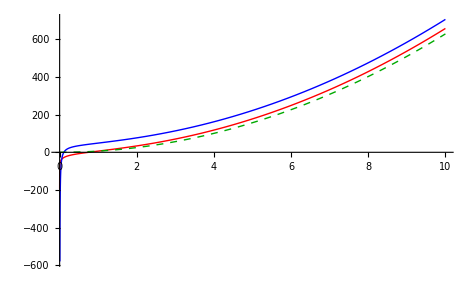

```mathematica
Plot[
Evaluate[{holoS,hαS, SSMS}//. {α-> Subscript[α, 0],Subscript[m, n]-> 1,n-> 0}],
{rH,0,10},
PlotStyle-> {Red,Blue,{Dashed,Darker@Green}}
]
```